```mathematica
eq1=A0[1]==0
```

A0[1]==0

```mathematica
eq2=-q1/(2 k1) y1^2+A0[1] y1+B0[1]==-q2/(2 k2) y1^2+A0[2] y1+B0[2]
```

-(q1 y1^2)/(2 k1)+y1 A0[1]+B0[1]==-(q2 y1^2)/(2 k2)+y1 A0[2]+B0[2]

```mathematica
eq3=-q1 y1+k1 A0[1]==-q2 y1+k2 A0[2]
```

-q1 y1+k1 A0[1]==-q2 y1+k2 A0[2]

```mathematica
eq4=-q2/(2 k2) y2^2+A0[2] y2+B0[2]==-q3/(2 k3) y2^2+A0[3] y2+B0[3]
```

-(q2 y2^2)/(2 k2)+y2 A0[2]+B0[2]==-(q3 y2^2)/(2 k3)+y2 A0[3]+B0[3]

```mathematica
eq5 = -q2 y2 + k2 A0[2] == -q3 y2 + k3 A0[3]
```

```mathematica
eq6 =-q3/(2k3)y3^2+A0[3]y3+B0[3]==-q4/(2k4)y3^2+A0[4]y3+B0[4]
```

-(q3 y3^2)/(2 k3)+y3 A0[3]+B0[3]==-(q4 y3^2)/(2 k4)+y3 A0[4]+B0[4]

```mathematica
eq7=-q3y3+k3A0[3]==-q4y3+k4A0[4]
```

-q3y3+k3A0[3]==-q4y3+k4A0[4]

```mathematica
eq8=-(q4/(2 k4)) y4^2+A0[4] y4+B0[4]==-(q5/(2 k5)) y4^2+A0[5] y4+B0[5]
```

-(q4 y4^2)/(2 k4)+y4 A0[4]+B0[4]==-(q5 y4^2)/(2 k5)+y4 A0[5]+B0[5]

```mathematica
eq9=-q4 y4+k4 A0[4]==-q5 y4+k5 A0[5]
```

-q4 y4+k4 A0[4]==-q5 y4+k5 A0[5]

```mathematica
eq10=-(q5/(2 k5)) y5^2+A0[5] y5+B0[5]==-(q6/(2 k6)) y5^2+A0[6] y5+B0[6]
```

-(q5 y5^2)/(2 k5)+y5 A0[5]+B0[5]==-(q6 y5^2)/(2 k6)+y5 A0[6]+B0[6]

```mathematica
eq11=-q5 y5+k5 A0[5]==-q6 y5+k6 A0[6]
```

-q5 y5+k5 A0[5]==-q6 y5+k6 A0[6]

```mathematica
eq12=-(q6/(2 k6)) y6^2+A0[6] y6+B0[6]==-(q7/(2 k7)) y6^2+A0[7] y6+B0[7]
```

-(q6 y6^2)/(2 k6)+y6 A0[6]+B0[6]==-(q7 y6^2)/(2 k7)+y6 A0[7]+B0[7]

```mathematica
eq13=-q6 y6+k6 A0[6]==-q7 y6+k7 A0[7]
```

-q6 y6+k6 A0[6]==-q7 y6+k7 A0[7]

```mathematica
eq14=-(q7/(2 k7)) y7^2+A0[7] y7+B0[7]==-(q8/(2 k8)) y7^2+A0[8] y7+B0[8]
```

-(q7 y7^2)/(2 k7)+y7 A0[7]+B0[7]==-(q8 y7^2)/(2 k8)+y7 A0[8]+B0[8]

```mathematica
eq15=-q7 y7+k7 A0[7]==-q8 y7+k8 A0[8]
```

```mathematica
-q7 y7+k7 A0[7]==-q8 y7+k8 A0[8]
```

```mathematica
eq16=-(q8/(2 k8)) y8^2+A0[8] y8+B0[8]==-(q9/(2 k9)) y8^2+A0[9] y8+B0[9]
```

-(q8 y8^2)/(2 k8)+y8 A0[8]+B0[8]==-(q9 y8^2)/(2 k9)+y8 A0[9]+B0[9]

```mathematica
eq17=-q8 y8+k8 A0[8]==-q9 y8+k9 A0[9]
```

-q8 y8+k8 A0[8]==-q9 y8+k9 A0[9]

```mathematica
eq18 = -(q9/k9)*y9+A0[9]== -(2*qr/w)*(b-a);
```

```mathematica
system={eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,eq10,eq11,eq12,eq13,eq14,eq15,eq16,eq17,eq18};
```

```mathematica
(* ===ПАРАМЕТРЫ===*)y1=1200*10^-9;y2=1420*10^-9;y3=1670*10^-9;y4=2320*10^-9;
y5=2362*10^-9;y6=3012*10^-9;y7=3162*10^-9;y8=3512*10^-9;y9=3682*10^-9;

k1=13.15;k2=46;k3=13.15;k4=46;k5=6;
k6=46;k7=13.15;k8=13.15;k9=35;

w=100*10^-6;a=25*10^-6;b=75*10^-6;qr=7.92*10^7;
f0target=2 qr (b-a)/w;(*целевой средний поток*)(*Источники:только активный слой (i=5)*)q1=0;q2=0;q3=0;q4=0;d5=42*10^-9;
q5=f0target/d5;(*предварительная оценка,потом уточним*)q6=0;q7=0;q8=0;q9=0;

(*Переменные*)
vars={A0[1],B0[1],A0[2],B0[2],A0[3],B0[3],A0[4],B0[4],A0[5],B0[5],A0[6],B0[6],A0[7],B0[7],A0[8],B0[8],A0[9],B0[9]};

(*Уравнения без верхнего условия (eq18)*)
eq1=A0[1]==0;
eqFix=B0[1]==0;
eq2=-(q1/(2 k1)) y1^2+A0[1] y1+B0[1]==-(q2/(2 k2)) y1^2+A0[2] y1+B0[2];
eq3=-q1 y1+k1 A0[1]==-q2 y1+k2 A0[2];
eq4=-(q2/(2 k2)) y2^2+A0[2] y2+B0[2]==-(q3/(2 k3)) y2^2+A0[3] y2+B0[3];
eq5=-q2 y2+k2 A0[2]==-q3 y2+k3 A0[3];
eq6=-(q3/(2 k3)) y3^2+A0[3] y3+B0[3]==-(q4/(2 k4)) y3^2+A0[4] y3+B0[4];
eq7=-q3 y3+k3 A0[3]==-q4 y3+k4 A0[4];
eq8=-(q4/(2 k4)) y4^2+A0[4] y4+B0[4]==-(q5/(2 k5)) y4^2+A0[5] y4+B0[5];
eq9=-q4 y4+k4 A0[4]==-q5 y4+k5 A0[5];
eq10=-(q5/(2 k5)) y5^2+A0[5] y5+B0[5]==-(q6/(2 k6)) y5^2+A0[6] y5+B0[6];
eq11=-q5 y5+k5 A0[5]==-q6 y5+k6 A0[6];
eq12=-(q6/(2 k6)) y6^2+A0[6] y6+B0[6]==-(q7/(2 k7)) y6^2+A0[7] y6+B0[7];
eq13=-q6 y6+k6 A0[6]==-q7 y6+k7 A0[7];
eq14=-(q7/(2 k7)) y7^2+A0[7] y7+B0[7]==-(q8/(2 k8)) y7^2+A0[8] y7+B0[8];
eq15=-q7 y7+k7 A0[7]==-q8 y7+k8 A0[8];
eq16=-(q8/(2 k8)) y8^2+A0[8] y8+B0[8]==-(q9/(2 k9)) y8^2+A0[9] y8+B0[9];
eq17=-q8 y8+k8 A0[8]==-q9 y8+k9 A0[9];

system={eq1,eqFix,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,eq10,eq11,eq12,eq13,eq14,eq15,eq16,eq17};

sol=NSolve[system,vars]
```

{{A0[1]→2.42571×10^-8,B0[1]→0.,A0[2]→6.93435×10^-9,B0[2]→7.15301×10^-15,A0[3]→2.42571×10^-8,B0[3]→3.14222×10^-15,A0[4]→6.93435×10^-9,B0[4]→-1.16663×10^-13,A0[5]→7.29143×10^8,B0[5]→-845.806,A0[6]→-1.72174×10^6,B0[6]→3.78955,A0[7]→-6.02281×10^6,B0[7]→16.7444,A0[8]→-6.02281×10^6,B0[8]→16.7444,A0[9]→-2.26286×10^6,B0[9]→3.53942}}

```mathematica
(* ===ЧИСЛЕННЫЕ ПАРАМЕТРЫ===*)(*Геометрия (координаты границ слоёв,м)*)y1=1200*10^-9;
y2=1420*10^-9;
y3=1670*10^-9;
y4=2320*10^-9;
y5=2362*10^-9;
y6=3012*10^-9;
y7=3162*10^-9;
y8=3512*10^-9;
y9=3682*10^-9;

(*Теплопроводности,Вт/(м·К)*)
k1=13.15;k2=46;k3=13.15;k4=46;k5=6;
k6=46;k7=13.15;k8=13.15;k9=35;

(*Параметры провода*)
w=100*10^-6;
a=25*10^-6;
b=75*10^-6;
qr=7.92*10^7;
f0=qr (b-a)/w;(*средний поток,положительный*)(*Источники тепла q_i (Вт/м.b3)—пока оценочные*)q1=1*10^12;
q2=1*10^12;
q3=1*10^12;
q4=1*10^12;
q5=1*10^12;
q6=1*10^12;
q7=1*10^12;
q8=1*10^12;
q9=1*10^12;

(* ===СИСТЕМА УРАВНЕНИЙ (17 уравнений)===*)

vars={A0[1],B0[1],A0[2],B0[2],A0[3],B0[3],A0[4],B0[4],A0[5],B0[5],A0[6],B0[6],A0[7],B0[7],A0[8],B0[8],A0[9],B0[9]};

(*Калибровка:фиксируем аддитивную константу*)
eqFix=B0[1]==0;

(*Стык 1-2*)
eq2=-(q1/(2 k1)) y1^2+A0[1] y1+B0[1]==-(q2/(2 k2)) y1^2+A0[2] y1+B0[2];
eq3=-q1 y1+k1 A0[1]==-q2 y1+k2 A0[2];

(*Стык 2-3*)
eq4=-(q2/(2 k2)) y2^2+A0[2] y2+B0[2]==-(q3/(2 k3)) y2^2+A0[3] y2+B0[3];
eq5=-q2 y2+k2 A0[2]==-q3 y2+k3 A0[3];

(*Стык 3-4*)
eq6=-(q3/(2 k3)) y3^2+A0[3] y3+B0[3]==-(q4/(2 k4)) y3^2+A0[4] y3+B0[4];
eq7=-q3 y3+k3 A0[3]==-q4 y3+k4 A0[4];

(*Стык 4-5*)
eq8=-(q4/(2 k4)) y4^2+A0[4] y4+B0[4]==-(q5/(2 k5)) y4^2+A0[5] y4+B0[5];
eq9=-q4 y4+k4 A0[4]==-q5 y4+k5 A0[5];

(*Стык 5-6*)
eq10=-(q5/(2 k5)) y5^2+A0[5] y5+B0[5]==-(q6/(2 k6)) y5^2+A0[6] y5+B0[6];
eq11=-q5 y5+k5 A0[5]==-q6 y5+k6 A0[6];

(*Стык 6-7*)
eq12=-(q6/(2 k6)) y6^2+A0[6] y6+B0[6]==-(q7/(2 k7)) y6^2+A0[7] y6+B0[7];
eq13=-q6 y6+k6 A0[6]==-q7 y6+k7 A0[7];

(*Стык 7-8*)
eq14=-(q7/(2 k7)) y7^2+A0[7] y7+B0[7]==-(q8/(2 k8)) y7^2+A0[8] y7+B0[8];
eq15=-q7 y7+k7 A0[7]==-q8 y7+k8 A0[8];

(*Стык 8-9*)
eq16=-(q8/(2 k8)) y8^2+A0[8] y8+B0[8]==-(q9/(2 k9)) y8^2+A0[9] y8+B0[9];
eq17=-q8 y8+k8 A0[8]==-q9 y8+k9 A0[9];

(*Верхнее условие (провод)*)
eq18=-(q9/k9) y9+A0[9]==f0;

system={eqFix,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,eq10,eq11,eq12,eq13,eq14,eq15,eq16,eq17,eq18};

(* ===РЕШЕНИЕ===*)

solution=NSolve[system,vars]
```

{{A0[1]→1.05679×10^8,B0[1]→0.,A0[2]→3.02105×10^7,B0[2]→90.5234,A0[3]→1.05679×10^8,B0[3]→-16.5875,A0[4]→3.02105×10^7,B0[4]→109.37,A0[5]→2.31614×10^8,B0[5]→-357.496,A0[6]→3.02105×10^7,B0[6]→117.814,A0[7]→1.05679×10^8,B0[7]→-109.251,A0[8]→1.05679×10^8,B0[8]→-109.251,A0[9]→3.97052×10^7,B0[9]→122.157}}

```mathematica
(*Извлекаем решение*)sol=solution[[1]];(*если решение выдано как список подстановок*)(*Определяем функцию температуры для каждого слоя*)T1[x_,y_]=-q1/(2 k1) y^2+(A0[1]/.sol) y+(B0[1]/.sol);
T2[x_,y_]=-q2/(2 k2) y^2+(A0[2]/.sol) y+(B0[2]/.sol);
T3[x_,y_]=-q3/(2 k3) y^2+(A0[3]/.sol) y+(B0[3]/.sol);
T4[x_,y_]=-q4/(2 k4) y^2+(A0[4]/.sol) y+(B0[4]/.sol);
T5[x_,y_]=-q5/(2 k5) y^2+(A0[5]/.sol) y+(B0[5]/.sol);
T6[x_,y_]=-q6/(2 k6) y^2+(A0[6]/.sol) y+(B0[6]/.sol);
T7[x_,y_]=-q7/(2 k7) y^2+(A0[7]/.sol) y+(B0[7]/.sol);
T8[x_,y_]=-q8/(2 k8) y^2+(A0[8]/.sol) y+(B0[8]/.sol);
T9[x_,y_]=-q9/(2 k9) y^2+(A0[9]/.sol) y+(B0[9]/.sol);

(*Собираем кусочно-определённую функцию по всей толщине*)
Ttotal[x_,y_]:=Piecewise[{{T1[x,y],0≤y≤y1},{T2[x,y],y1<y≤y2},{T3[x,y],y2<y≤y3},{T4[x,y],y3<y≤y4},{T5[x,y],y4<y≤y5},{T6[x,y],y5<y≤y6},{T7[x,y],y6<y≤y7},{T8[x,y],y7<y≤y8},{T9[x,y],y8<y≤y9}}]

(*Пример:профиль температуры по центру (x=w/2)*)
Plot[Ttotal[w/2,y*10^9],{y,0,y9*10^9},AxesLabel->{"y (нм)","T(y) (K)"},PlotLabel->"Температура по центру структуры (x = w/2)",GridLines->Automatic,PlotRange->All]
```

```mathematica
DensityPlot[Ttotal[x*10^6,y*10^9],{x,0,w*10^6},{y,0,y9*10^9},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"x (мкм)","y (нм)"},PlotLabel->"Распределение температуры T(x,y)",AspectRatio->0.5]
```

```mathematica
(* ===ЧИСЛЕННЫЕ ПАРАМЕТРЫ===*)(*Геометрия (координаты границ слоёв,м)*)y1=1200*10^-9;
y2=1420*10^-9;
y3=1670*10^-9;
y4=2320*10^-9;
y5=2362*10^-9;
y6=3012*10^-9;
y7=3162*10^-9;
y8=3512*10^-9;
y9=3682*10^-9;

(*Теплопроводности,Вт/(м·К)*)
k1=13.15;k2=46;k3=13.15;k4=46;k5=6;
k6=46;k7=13.15;k8=13.15;k9=35;

(*Параметры провода*)
w=100*10^-6;
a=25*10^-6;
b=75*10^-6;
qr=7.92*10^7;
f0=qr (b-a)/w;(*средний поток,положительный*)(*Источники тепла q_i (Вт/м.b3)—пока оценочные*)

q1=1*10^12;
q2=1*10^13;
q3=1*10^13;
q4=1*10^13;
q5=1*10^13;
q6=1*10^13;
q7=1*10^13;
q8=1*10^13;
q9=1*10^13;

(* ===СИСТЕМА УРАВНЕНИЙ (18×18)===*)

vars={A0[1],B0[1],A0[2],B0[2],A0[3],B0[3],A0[4],B0[4],A0[5],B0[5],A0[6],B0[6],A0[7],B0[7],A0[8],B0[8],A0[9],B0[9]};

(*Калибровка:фиксируем аддитивную константу*)
eqFix=B0[1]==0;

(*Стык 1-2*)
eq2=-(q1/(2 k1)) y1^2+A0[1] y1+B0[1]==-(q2/(2 k2)) y1^2+A0[2] y1+B0[2];
eq3=-q1 y1+k1 A0[1]==-q2 y1+k2 A0[2];

(*Стык 2-3*)
eq4=-(q2/(2 k2)) y2^2+A0[2] y2+B0[2]==-(q3/(2 k3)) y2^2+A0[3] y2+B0[3];
eq5=-q2 y2+k2 A0[2]==-q3 y2+k3 A0[3];

(*Стык 3-4*)
eq6=-(q3/(2 k3)) y3^2+A0[3] y3+B0[3]==-(q4/(2 k4)) y3^2+A0[4] y3+B0[4];
eq7=-q3 y3+k3 A0[3]==-q4 y3+k4 A0[4];

(*Стык 4-5*)
eq8=-(q4/(2 k4)) y4^2+A0[4] y4+B0[4]==-(q5/(2 k5)) y4^2+A0[5] y4+B0[5];
eq9=-q4 y4+k4 A0[4]==-q5 y4+k5 A0[5];

(*Стык 5-6*)
eq10=-(q5/(2 k5)) y5^2+A0[5] y5+B0[5]==-(q6/(2 k6)) y5^2+A0[6] y5+B0[6];
eq11=-q5 y5+k5 A0[5]==-q6 y5+k6 A0[6];

(*Стык 6-7*)
eq12=-(q6/(2 k6)) y6^2+A0[6] y6+B0[6]==-(q7/(2 k7)) y6^2+A0[7] y6+B0[7];
eq13=-q6 y6+k6 A0[6]==-q7 y6+k7 A0[7];

(*Стык 7-8*)
eq14=-(q7/(2 k7)) y7^2+A0[7] y7+B0[7]==-(q8/(2 k8)) y7^2+A0[8] y7+B0[8];
eq15=-q7 y7+k7 A0[7]==-q8 y7+k8 A0[8];

(*Стык 8-9*)
eq16=-(q8/(2 k8)) y8^2+A0[8] y8+B0[8]==-(q9/(2 k9)) y8^2+A0[9] y8+B0[9];
eq17=-q8 y8+k8 A0[8]==-q9 y8+k9 A0[9];

(*Верхнее условие (провод)*)
eq18=-(q9/k9) y9+A0[9]==f0;

system={eqFix,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,eq10,eq11,eq12,eq13,eq14,eq15,eq16,eq17,eq18};

(* ===РЕШЕНИЕ===*)
solution=NSolve[system,vars][[1]]

(* ===ПОСТРОЕНИЕ===*)

(*Определяем функцию температуры для каждого слоя*)
T1[x_,y_]=-q1/(2 k1) y^2+(A0[1]/.solution) y+(B0[1]/.solution);
T2[x_,y_]=-q2/(2 k2) y^2+(A0[2]/.solution) y+(B0[2]/.solution);
T3[x_,y_]=-q3/(2 k3) y^2+(A0[3]/.solution) y+(B0[3]/.solution);
T4[x_,y_]=-q4/(2 k4) y^2+(A0[4]/.solution) y+(B0[4]/.solution);
T5[x_,y_]=-q5/(2 k5) y^2+(A0[5]/.solution) y+(B0[5]/.solution);
T6[x_,y_]=-q6/(2 k6) y^2+(A0[6]/.solution) y+(B0[6]/.solution);
T7[x_,y_]=-q7/(2 k7) y^2+(A0[7]/.solution) y+(B0[7]/.solution);
T8[x_,y_]=-q8/(2 k8) y^2+(A0[8]/.solution) y+(B0[8]/.solution);
T9[x_,y_]=-q9/(2 k9) y^2+(A0[9]/.solution) y+(B0[9]/.solution);

(*Кусочная функция по всей толщине*)
Ttotal[x_,y_]:=Piecewise[{{T1[x,y],0≤y≤y1},{T2[x,y],y1<y≤y2},{T3[x,y],y2<y≤y3},{T4[x,y],y3<y≤y4},{T5[x,y],y4<y≤y5},{T6[x,y],y5<y≤y6},{T7[x,y],y6<y≤y7},{T8[x,y],y7<y≤y8},{T9[x,y],y8<y≤y9}}]

(* ===1. Профиль температуры по центру (x=w/2)===*)
Plot[Ttotal[w/2,y*10^9],{y,0,y9*10^9},AxesLabel->{"y (нм)","T (K)"},PlotLabel->"Температура по центру структуры (x = w/2)",GridLines->Automatic,PlotRange->All,ImageSize->Large]

(* ===2. 2D тепловая карта===*)
DensityPlot[Ttotal[x*10^6,y*10^9],{x,0,w*10^6},{y,0,y9*10^9},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"x (мкм)","y (нм)"},PlotLabel->"Распределение температуры T(x,y)",AspectRatio->0.5,ImageSize->Large,ClippingStyle->Automatic]
```

{A0[1]→1.07378×10^8,B0[1]→0.,A0[2]→3.09309×10^7,B0[2]→91.8383,A0[3]→1.08199×10^8,B0[3]→-17.3353,A0[4]→3.09309×10^7,B0[4]→110.946,A0[5]→2.37137×10^8,B0[5]→-363.552,A0[6]→3.09309×10^7,B0[6]→119.464,A0[7]→1.08199×10^8,B0[7]→-110.805,A0[8]→1.08199×10^8,B0[8]→-110.805,A0[9]→4.0652×10^7,B0[9]→123.493}

```mathematica
(* ===ВЫЧИСЛЕНИЕ ТЕМПЕРАТУРЫ НА ГРАНИЦАХ СЛОЁВ===*)(*Задаём x,для которого считаем*)x0=w/2;(*можно заменить на 0,w/2,w*)Print["x = ",x0*10^6," мкм"];

(*Частное решение на границах слоёв*)
Print["\nЧАСТНОЕ РЕШЕНИЕ (n=0):"];
Print["y = 0:      T = ",B0[1]/.sol0];
Print["y = y1:     T = ",q1/(2 k1) y1^2+(A0[1]) y1+(B0[1])];
Print["y = y2:     T = ",q2/(2 k2) y2^2+(A0[2]) y2+(B0[2])];
Print["y = y3:     T = ",q3/(2 k3) y3^2+(A0[3]) y3+(B0[3])];
Print["y = y4:     T = ",q4/(2 k4) y4^2+(A0[4]) y4+(B0[4])];
Print["y = y5:     T = ",q5/(2 k5) y5^2+(A0[5]) y5+(B0[5])];
Print["y = y6:     T = ",q6/(2 k6) y6^2+(A0[6]) y6+(B0[6])];
Print["y = y7:     T = ",q7/(2 k7) y7^2+(A0[7]) y7+(B0[7])];
Print["y = y8:     T = ",q8/(2 k8) y8^2+(A0[8]) y8+(B0[8])];
Print["y = y9:     T = ",q9/(2 k9) y9^2+(A0[9]) y9+(B0[9])];

(*Однородные моды на границах слоёв*)
Print["\nВКЛАД ОДНОРОДНЫХ МОД ПРИ x = ",x0*10^6," мкм:"];

(*Функция для вычисления вклада всех мод в точке (x,y)*)
ThPoint[x_,y_]:=Sum[Module[{n=s[[1]],α=(π s[[1]])/w,sol=s[[2]]},((An[1]/.sol) Sinh[α y]+(Bn[1]/.sol) Cosh[α y]) Cos[α x]],{s,solsN}];

Print["y = 0:      Th = ",ThPoint[x0,0]];
Print["y = y1:     Th = ",ThPoint[x0,y1]];
Print["y = y2:     Th = ",ThPoint[x0,y2]];
Print["y = y3:     Th = ",ThPoint[x0,y3]];
Print["y = y4:     Th = ",ThPoint[x0,y4]];
Print["y = y5:     Th = ",ThPoint[x0,y5]];
Print["y = y6:     Th = ",ThPoint[x0,y6]];
Print["y = y7:     Th = ",ThPoint[x0,y7]];
Print["y = y8:     Th = ",ThPoint[x0,y8]];
Print["y = y9:     Th = ",ThPoint[x0,y9]];

(*Полная температура на границах слоёв*)
Print["\nПОЛНАЯ ТЕМПЕРАТУРА (частное + моды) ПРИ x = ",x0*10^6," мкм:"];
Print["y = 0:      T = ",(B0[1])+ThPoint[x0,0]];
Print["y = y1:     T = ",(q1/(2 k1) y1^2+(A0[1]) y1+(B0[1]))+ThPoint[x0,y1]];
Print["y = y2:     T = ",(q2/(2 k2) y2^2+(A0[2]) y2+(B0[2]))+ThPoint[x0,y2]];
Print["y = y3:     T = ",(q3/(2 k3) y3^2+(A0[3]) y3+(B0[3]))+ThPoint[x0,y3]];
Print["y = y4:     T = ",(q4/(2 k4) y4^2+(A0[4]) y4+(B0[4]))+ThPoint[x0,y4]];
Print["y = y5:     T = ",(q5/(2 k5) y5^2+(A0[5]) y5+(B0[5]))+ThPoint[x0,y5]];
Print["y = y6:     T = ",(q6/(2 k6) y6^2+(A0[6]) y6+(B0[6]))+ThPoint[x0,y6]];
Print["y = y7:     T = ",(q7/(2 k7) y7^2+(A0[7]) y7+(B0[7]))+ThPoint[x0,y7]];
Print["y = y8:     T = ",(q8/(2 k8) y8^2+(A0[8]) y8+(B0[8]))+ThPoint[x0,y8]];
Print["y = y9:     T = ",(q9/(2 k9) y9^2+(A0[9]) y9+(B0[9]))+ThPoint[x0,y9]];
```

x = 200 мкм

ЧАСТНОЕ РЕШЕНИЕ (n=0):

y = 0:      T = 0.

y = y1:     T = 0.000319418+(3 A0[1])/2500000+B0[1]

y = y2:     T = 0.000512166+(71 A0[2])/50000000+B0[2]

y = y3:     T = 0.0136238+(167 A0[3])/100000000+B0[3]

y = y4:     T = 0.0149239+(29 A0[4])/12500000+B0[4]

y = y5:     T = 5.98479+(1181 A0[5])/500000000+B0[5]

y = y6:     T = 0.0134433+(753 A0[6])/250000000+B0[6]

y = y7:     T = 0.0271452+(1581 A0[7])/500000000+B0[7]

y = y8:     T = 0.00937395+(439 A0[8])/125000000+B0[8]

y = y9:     T = 0.000107348+(1841 A0[9])/500000000+B0[9]

ВКЛАД ОДНОРОДНЫХ МОД ПРИ x = 200 мкм:

y = 0:      Th = 378.196

y = y1:     Th = 378.289

y = y2:     Th = 378.327

y = y3:     Th = 378.377

y = y4:     Th = 378.545

y = y5:     Th = 378.558

y = y6:     Th = 378.785

y = y7:     Th = 378.845

y = y8:     Th = 378.997

y = y9:     Th = 379.077

ПОЛНАЯ ТЕМПЕРАТУРА (частное + моды) ПРИ x = 200 мкм:

y = 0:      T = 378.196+B0[1]

y = y1:     T = 378.289+(3 A0[1])/2500000+B0[1]

y = y2:     T = 378.327+(71 A0[2])/50000000+B0[2]

y = y3:     T = 378.39+(167 A0[3])/100000000+B0[3]

y = y4:     T = 378.56+(29 A0[4])/12500000+B0[4]

y = y5:     T = 384.543+(1181 A0[5])/500000000+B0[5]

y = y6:     T = 378.798+(753 A0[6])/250000000+B0[6]

y = y7:     T = 378.872+(1581 A0[7])/500000000+B0[7]

y = y8:     T = 379.007+(439 A0[8])/125000000+B0[8]

y = y9:     T = 379.077+(1841 A0[9])/500000000+B0[9]

Температура на границах слоёв (x = w/2):

y = 0      : T = 0. K

y = y1     : T = 0.0335594 K

y = y2     : T = 0.0679915 K

y = y3     : T = 0.081653 K

y = y4     : T = 0.0992231 K

y = y5     : T = -11.8372 K

y = y6     : T = 0.185995 K

y = y7     : T = 0.261669 K

y = y8     : T = 0.537962 K

y = y9     : T = 0.577765 K

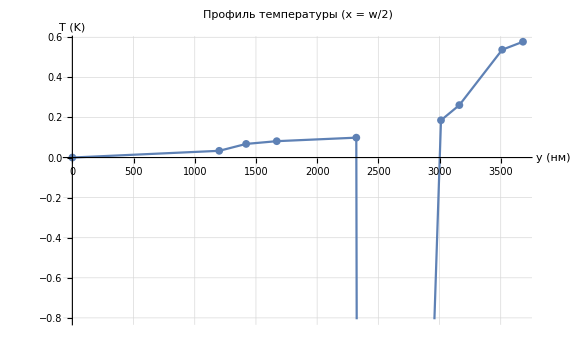

```mathematica
(* ==========ВСПОМОГАТЕЛЬНЫЙ КОД==========*)(*Использует готовое решение sol0 для расчёта температуры*)(*Функция температуры в слое i в точке y*)Tlayer[i_,y_]:=-q[[i]]/(2 k[[i]]) y^2+(A0[i]/.sol0) y+(B0[i]/.sol0)

(*Массивы для удобства*)
q={q1,q2,q3,q4,q5,q6,q7,q8,q9};
k={k1,k2,k3,k4,k5,k6,k7,k8,k9};
yBoundary={0,y1,y2,y3,y4,y5,y6,y7,y8,y9};

(*Вычисляем температуру на каждой границе*)
temperatures=Table[Which[y==0,Tlayer[1,0],y==y1,Tlayer[1,y1],y==y2,Tlayer[2,y2],y==y3,Tlayer[3,y3],y==y4,Tlayer[4,y4],y==y5,Tlayer[5,y5],y==y6,Tlayer[6,y6],y==y7,Tlayer[7,y7],y==y8,Tlayer[8,y8],y==y9,Tlayer[9,y9]],{y,yBoundary}];

(*Вывод в консоль*)
Print["Температура на границах слоёв (x = w/2):"];
Print["y = 0      : T = ",temperatures[[1]]," K"];
Print["y = y1     : T = ",temperatures[[2]]," K"];
Print["y = y2     : T = ",temperatures[[3]]," K"];
Print["y = y3     : T = ",temperatures[[4]]," K"];
Print["y = y4     : T = ",temperatures[[5]]," K"];
Print["y = y5     : T = ",temperatures[[6]]," K"];
Print["y = y6     : T = ",temperatures[[7]]," K"];
Print["y = y7     : T = ",temperatures[[8]]," K"];
Print["y = y8     : T = ",temperatures[[9]]," K"];
Print["y = y9     : T = ",temperatures[[10]]," K"];

(*Построение графика*)
points=Transpose[{yBoundary*10^9,temperatures}];
ListPlot[points,Joined->True,PlotMarkers->{Automatic,8},AxesLabel->{"y (нм)","T (K)"},PlotLabel->"Профиль температуры (x = w/2)",GridLines->Automatic,ImageSize->Large]
```

```mathematica
(* ===ВЫЧИСЛЕНИЕ ТЕМПЕРАТУРЫ НА ГРАНИЦАХ СЛОЁВ===*)(*Задаём x,для которого считаем*)x0=w/2;(*можно заменить на 0,w/2,w*)Print["x = ",x0*10^6," мкм"];

(*Частное решение на границах слоёв*)
Print["\nЧАСТНОЕ РЕШЕНИЕ (n=0):"];
Print["y = 0      : T = ",(B0[1]/.sol0)];
Print["y = y1     : T = ",(-q1/(2 k1) y1^2+(A0[1]/.sol0) y1+(B0[1]/.sol0))];
Print["y = y2     : T = ",(-q2/(2 k2) y2^2+(A0[2]/.sol0) y2+(B0[2]/.sol0))];
Print["y = y3     : T = ",(-q3/(2 k3) y3^2+(A0[3]/.sol0) y3+(B0[3]/.sol0))];
Print["y = y4     : T = ",(-q4/(2 k4) y4^2+(A0[4]/.sol0) y4+(B0[4]/.sol0))];
Print["y = y5     : T = ",(-q5/(2 k5) y5^2+(A0[5]/.sol0) y5+(B0[5]/.sol0))];
Print["y = y6     : T = ",(-q6/(2 k6) y6^2+(A0[6]/.sol0) y6+(B0[6]/.sol0))];
Print["y = y7     : T = ",(-q7/(2 k7) y7^2+(A0[7]/.sol0) y7+(B0[7]/.sol0))];
Print["y = y8     : T = ",(-q8/(2 k8) y8^2+(A0[8]/.sol0) y8+(B0[8]/.sol0))];
Print["y = y9     : T = ",(-q9/(2 k9) y9^2+(A0[9]/.sol0) y9+(B0[9]/.sol0))];

(*Если есть однородные моды—выводим их вклад*)
If[ValueQ[solsN]&&solsN=!={},Print["\nВКЛАД ОДНОРОДНЫХ МОД ПРИ x = ",x0*10^6," мкм:"];
(*Функция для вычисления вклада всех мод в точке (x,y)*)ThPoint[x_,y_]:=Sum[Module[{n=s[[1]],α=(π s[[1]])/w,sol=s[[2]]},((An[1]/.sol) Sinh[α y]+(Bn[1]/.sol) Cosh[α y]) Cos[α x]],{s,solsN}];
Print["y = 0      : Th = ",ThPoint[x0,0]];
Print["y = y1     : Th = ",ThPoint[x0,y1]];
Print["y = y2     : Th = ",ThPoint[x0,y2]];
Print["y = y3     : Th = ",ThPoint[x0,y3]];
Print["y = y4     : Th = ",ThPoint[x0,y4]];
Print["y = y5     : Th = ",ThPoint[x0,y5]];
Print["y = y6     : Th = ",ThPoint[x0,y6]];
Print["y = y7     : Th = ",ThPoint[x0,y7]];
Print["y = y8     : Th = ",ThPoint[x0,y8]];
Print["y = y9     : Th = ",ThPoint[x0,y9]];
Print["\nПОЛНАЯ ТЕМПЕРАТУРА (частное + моды) ПРИ x = ",x0*10^6," мкм:"];
Print["y = 0      : T = ",(B0[1]/.sol0)+ThPoint[x0,0]];
Print["y = y1     : T = ",(-q1/(2 k1) y1^2+(A0[1]/.sol0) y1+(B0[1]/.sol0))+ThPoint[x0,y1]];
Print["y = y2     : T = ",(-q2/(2 k2) y2^2+(A0[2]/.sol0) y2+(B0[2]/.sol0))+ThPoint[x0,y2]];
Print["y = y3     : T = ",(-q3/(2 k3) y3^2+(A0[3]/.sol0) y3+(B0[3]/.sol0))+ThPoint[x0,y3]];
Print["y = y4     : T = ",(-q4/(2 k4) y4^2+(A0[4]/.sol0) y4+(B0[4]/.sol0))+ThPoint[x0,y4]];
Print["y = y5     : T = ",(-q5/(2 k5) y5^2+(A0[5]/.sol0) y5+(B0[5]/.sol0))+ThPoint[x0,y5]];
Print["y = y6     : T = ",(-q6/(2 k6) y6^2+(A0[6]/.sol0) y6+(B0[6]/.sol0))+ThPoint[x0,y6]];
Print["y = y7     : T = ",(-q7/(2 k7) y7^2+(A0[7]/.sol0) y7+(B0[7]/.sol0))+ThPoint[x0,y7]];
Print["y = y8     : T = ",(-q8/(2 k8) y8^2+(A0[8]/.sol0) y8+(B0[8]/.sol0))+ThPoint[x0,y8]];
Print["y = y9     : T = ",(-q9/(2 k9) y9^2+(A0[9]/.sol0) y9+(B0[9]/.sol0))+ThPoint[x0,y9]];,Print["\n(Однородные моды не найдены или не заданы.)"]]
```

x = 200 мкм

ЧАСТНОЕ РЕШЕНИЕ (n=0):

y = 0      : T = 0.

y = y1     : T = 0.265942

y = y2     : T = 0.533765

y = y3     : T = 0.837791

y = y4     : T = 0.980196

y = y5     : T = 0.98743

y = y6     : T = 1.06947

y = y7     : T = 1.17273

y = y8     : T = 1.41346

y = y9     : T = 1.43471

ВКЛАД ОДНОРОДНЫХ МОД ПРИ x = 200 мкм:

y = 0      : Th = 378.196

y = y1     : Th = 378.289

y = y2     : Th = 378.327

y = y3     : Th = 378.377

y = y4     : Th = 378.545

y = y5     : Th = 378.558

y = y6     : Th = 378.785

y = y7     : Th = 378.845

y = y8     : Th = 378.997

y = y9     : Th = 379.077

ПОЛНАЯ ТЕМПЕРАТУРА (частное + моды) ПРИ x = 200 мкм:

y = 0      : T = 378.196

y = y1     : T = 378.555

y = y2     : T = 378.86

y = y3     : T = 379.215

y = y4     : T = 379.525

y = y5     : T = 379.545

y = y6     : T = 379.854

y = y7     : T = 380.018

y = y8     : T = 380.411

y = y9     : T = 380.512

```mathematica
(* ==========ФИЗИЧЕСКИЕ ПАРАМЕТРЫ==========*)w=400*10^-6;
L=4*10^-3;

y1=1200*10^-9;y2=1420*10^-9;y3=1670*10^-9;y4=2320*10^-9;
y5=2362*10^-9;y6=3012*10^-9;y7=3162*10^-9;y8=3512*10^-9;y9=3682*10^-9;

k1=55;k2=10;k3=10;k4=55;k5=55;
k6=55;k7=10;k8=10;k9=55;

q1=-2.44*10^10;q2=-5.08*10^9;q3=-9.77*10^10;q4=-3.05*10^11;
q5=-1.18*10^14;
q6=-1.63*10^11;q7=-5.43*10^10;q8=-1.52*10^10;q9=-8.71*10^8;

a=150*10^-6;b=250*10^-6;qr=-5*10^5;
f0=qr (b-a)/w;

(* ==========СИСТЕМА ДЛЯ ЧАСТНОГО РЕШЕНИЯ (n=0)==========*)

vars0={A0[1],B0[1],A0[2],B0[2],A0[3],B0[3],A0[4],B0[4],A0[5],B0[5],A0[6],B0[6],A0[7],B0[7],A0[8],B0[8],A0[9],B0[9]};

(*Нижнее условие:теплоизоляция*)
eq1=B0[1]==0; 

(*Стык 1-2*)
eq2=q1/(2 k1) y1^2+A0[1] y1+B0[1]==q2/(2 k2) y1^2+A0[2] y1+B0[2];
eq3=q1 y1+k1 A0[1]==q2 y1+k2 A0[2];

(*Стык 2-3*)
eq4=q2/(2 k2) y2^2+A0[2] y2+B0[2]==q3/(2 k3) y2^2+A0[3] y2+B0[3];
eq5=q2 y2+k2 A0[2]==q3 y2+k3 A0[3];

(*Стык 3-4*)
eq6=q3/(2 k3) y3^2+A0[3] y3+B0[3]==q4/(2 k4) y3^2+A0[4] y3+B0[4];
eq7=q3 y3+k3 A0[3]==q4 y3+k4 A0[4];

(*Стык 4-5*)
eq8=q4/(2 k4) y4^2+A0[4] y4+B0[4]==q5/(2 k5) y4^2+A0[5] y4+B0[5];
eq9=q4 y4+k4 A0[4]==q5 y4+k5 A0[5];

(*Стык 5-6*)
eq10=q5/(2 k5) y5^2+A0[5] y5+B0[5]==q6/(2 k6) y5^2+A0[6] y5+B0[6];
eq11=q5 y5+k5 A0[5]==q6 y5+k6 A0[6];

(*Стык 6-7*)
eq12=q6/(2 k6) y6^2+A0[6] y6+B0[6]==q7/(2 k7) y6^2+A0[7] y6+B0[7];
eq13=q6 y6+k6 A0[6]==q7 y6+k7 A0[7];

(*Стык 7-8*)
eq14=q7/(2 k7) y7^2+A0[7] y7+B0[7]==q8/(2 k8) y7^2+A0[8] y7+B0[8];
eq15=q7 y7+k7 A0[7]==q8 y7+k8 A0[8];

(*Стык 8-9*)
eq16=q8/(2 k8) y8^2+A0[8] y8+B0[8]==q9/(2 k9) y8^2+A0[9] y8+B0[9];
eq17=q8 y8+k8 A0[8]==q9 y8+k9 A0[9];

(*Верхнее условие:поток от провода (без лишнего минуса)*)
eq18=q9/k9 y9+A0[9]==f0;

system0={eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,eq10,eq11,eq12,eq13,eq14,eq15,eq16,eq17,eq18};

sol0=NSolve[system0,vars0][[1]]
```

{A0[1]→-28115.7,B0[1]→0.,A0[2]→-156955.,B0[2]→0.154653,A0[3]→-143803.,B0[3]→0.145315,A0[4]→-19851.6,B0[4]→-0.0675741,A0[5]→4.94474×10^6,B0[5]→-5.8265,A0[6]→-115826.,B0[6]→0.150028,A0[7]→-669784.,B0[7]→1.82974,A0[8]→-682147.,B0[8]→1.84928,A0[9]→-124942.,B0[9]→-0.116899}